## Initialization Code

```mathematica
(*physics constants*)
qe = 1.60217663*10^-19;
e0 = 8.8541878188*10^-12;
amu = 1.66053904*10^-27;
h = 6.62607015*10^-34;
ℏ = h/(2*π);

(*trap parameters*)
r0 = 550 * μm;

(*distance units*)
nm = 10^-9;
μm = 10^-6;
mm = 10^-3;

(*frequency units*)
Hz = 1;
kHz = 10^3;
MHz = 10^6;
GHz = 10^9;


(*All masses are in units of amu*)
mCa = 39.962590863;
mElectron = 0.0005486; 
mCaIon = mCa - mElectron; 
mH = 1.007825032; 
mHClAcc = 35.97555342; (*Grant's Number*)
mCl35 = 34.968852;
mHCl35 = mH + mCl35 - mElectron; 
mCl37 = 36.9659023;
mHCl37 = mH + mCl37 - mElectron;
mH2Cl37 = 2*mH + mCl37 - mElectron;
```

```mathematica
(*Calculate mass independent mathieu equations*)
getMathieuParams[knownSecFreqs_, knownMass_, ΩRF_]:= Module[{knownSecFreqsSorted, ar, az, qx},
knownSecFreqsSorted = knownSecFreqs[[Ordering[knownSecFreqs]]];
(*get source for these formulas*)
ar = 2/ΩRF^2*(knownSecFreqsSorted[[3]]^2-knownSecFreqsSorted[[2]]^2);
az = 4/ΩRF^2*knownSecFreqsSorted[[1]]^2;
qx = Sqrt[8*knownSecFreqsSorted[[3]]^2/ΩRF^2-(ar-2*az)];
{ar, az, qx}*knownMass
]
```

```mathematica
(*convert the mathieu parameters to be independent of mass*)
getMassIndepSecFreqs[massIndepMathieuParams_, massArr_, ΩRF_]:= Module[{arMassIndep, azMassIndep, qxMassIndep,
independentAxialFreqs, independentEGGsFreqs, independentRFFreqs},
arMassIndep = massIndepMathieuParams[[1]];
azMassIndep = massIndepMathieuParams[[2]];
qxMassIndep = massIndepMathieuParams[[3]];
independentAxialFreqs = Sqrt[azMassIndep/massArr*ΩRF^2/4];
independentEGGsFreqs = Sqrt[((qxMassIndep/massArr)^2+(arMassIndep/massArr-2*azMassIndep/massArr))*ΩRF^2/8];
independentRFFreqs= Sqrt[independentEGGsFreqs^2-ΩRF^2/2*arMassIndep/massArr];
{independentAxialFreqs, independentRFFreqs, independentEGGsFreqs}]
```

```mathematica
getPotential[massArr_, massIndepSecFreqs_, numIons_, EField_, ionPositions_, β_:0, γ_:0, δ_:0]:=Module[
{independentAxialFreqs, independentEGGsFreqs,independentRFFreqs,
Utrap, UColoumb, UField, Uanharmonic, U, EFieldMat,
Ucubic, Uquartic, Uquintic},

EFieldMat =ConstantArray[EField, numIons];
independentAxialFreqs = massIndepSecFreqs[[1]];
independentRFFreqs = massIndepSecFreqs[[2]];
independentEGGsFreqs = massIndepSecFreqs[[3]];

(*construct harmonic trap potential*)
Utrap = Sum[massArr[[i]]/2*amu*(independentRFFreqs[[i]]^2*x[i]^2+independentEGGsFreqs[[i]]^2*y[i]^2+independentAxialFreqs[[i]]^2*z[i]^2), {i, 1, numIons}];

(*construct ion-ion electrical repulsion - assume all ions are singly charged*)
UColoumb = qe^2/(4*π*e0)*Sum[Sum[ 1/Sqrt[(x[i]-x[j])^2+(y[i]-y[j])^2+(z[i]-z[j])^2], {i,1, j-1}], {j, 1, numIons}];

(*construct potential from uniform field - assume all ions are singly charged*)
UField = -qe*Total[Flatten[ionPositions*EFieldMat]];

(*Construct anharmonic terms up to 5th order*)
Ucubic = Sum[qe*β*z[i]^3, {i, 1, numIons}];
Uquartic = Sum[qe*γ*z[i]^4, {i, 1, numIons}];
Uquintic = + Sum[qe*δ*z[i]^5, {i, 1, numIons}];
Uanharmonic = Ucubic + Uquartic + Uquintic; 

(*add and return sum of potential terms*)
U = Utrap + UColoumb + UField + Uanharmonic;
U
]
```

```mathematica
getEquilibriumPositions[U_,numIons_, ionEqPositions_] :=Module[
{zGuess, guessPositions, ionEquilibriumPositions}, 

(*Start with guess where ions are spaced 10 mincrons apart and lie along z-axis - heuristic*)
zGuess = 10*Flatten[Table[{i}, {i, -(numIons-1)/2, (numIons-1)/2,1}]]*μm;
guessPositions = Flatten[Table[{{z[i],zGuess[[i]]}, {y[i],0}, {x[i],0}}, {i,1,numIons}],1];

(*Solve ion equilibrium positions via force equation - i.e. solve coordinates which make first derivative of potential 0*)
ionEquilibriumPositions = FindRoot[Table[D[U, q]==0, {q, Flatten[ionEqPositions]}],guessPositions];

(*return results*)
ionEquilibriumPositions]
```

```mathematica
getModeParams[U_, massArr_, ionEquilibriumPositions_, numIons_,ionPositions_]:= Module[
{evals, evecs,
M, H, orderingIndices, evecsSorted, 
evecsNormalized, evalsSorted, secFreqsMHz, hessianMassWeighted},

(*construct Hessian - matrix of second derivative of potential w.r.t ion positions*)
H = D[U, {Flatten[ionPositions], 2}]/.ionEquilibriumPositions;

(*create mass array in and move to mass-weight coordinates*)
M = DiagonalMatrix[Flatten[Table[massArr[[i]]*amu*{1,1,1}, {i, numIons}]]];
hessianMassWeighted = Sqrt[Inverse[M]].H.Sqrt[Inverse[M]];

(*diagonalize mass-weighted hessian to solve for eigenvectors (mode parameters) and eigenfrequencies*)
{evals, evecs} = Eigensystem[hessianMassWeighted];
orderingIndices = Ordering[evals];
evecsSorted = evecs[[orderingIndices]];

(*Normalize eigenvectors - chop turns numbers close to 0 to 0, i.e. eliminates weird floating points remanants*)
evecsNormalized = Chop[Table[Normalize[evecsSorted[[idx]]], {idx, Length[evecsSorted]}]];
evalsSorted = evals[[orderingIndices]];
secFreqsMHz = Chop[Sqrt[evalsSorted]/(2*π*MHz)];

(*return results*)
{evecsNormalized, secFreqsMHz}
]
```

```mathematica
overlapScore[axialRock_, vec_] := Abs[Conjugate[axialRock].vec]^2
getAxialRock[{vecs_, vals_}]:= Module[{axialRockBasis, scores, idx},
axialRockBasis = {0,0,-1,0,0,1,0,0,-1};
scores = overlapScore[axialRockBasis, #] & /@ vecs;
idx = First @ Ordering[scores, -1];
vals[[idx]]
]
```

```mathematica
SimDiffSecFreqs[Sec1_, Sec2_, Sec3_, voltRange_:20]:=Module[
{singleIonSecFreqs, SecFreqs, maxSecFreqShift, simVoltageList, secFreqs},

(*convert single ion secs from rads to MHz*)
singleIonSecFreqs = 2*π*MHz*{Sec1, Sec2, Sec3};


(*create a voltage scan about a provided center point*)
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,voltRange/10}];

(* Convert voltage scan to electric field the ion sees 
κProjection is a magic number from what I gather
assume voltage produces equal electric field aong both axes*)
κProjection = 0.077;
secFreqs = Table[getAxialRock[getSecFreqs[{(κProjection*(Volt-voltMidPoint))/Sqrt[2],(κProjection*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, singleIonSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];

(* reutrn results in Hz *)
maxSecFreqShift = (Max[secFreqs] - Min[secFreqs]);
maxSecFreqShift*MHz
]
```

```mathematica
getSecFreqs[EField_, massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, β_:0, γ_:0, δ_:0]:= Module[
{massIndepMathieuParams, 
massIndepSecFreqs, U, evecsNormalized, secFreqsMHz, ionEqPositions},


(*determine mathieu par*)
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];

(*construct potential and obtain equilibrium positions and mode parameters*)
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, β, γ, δ];
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions] (*this must be a different name*);
{evecsNormalized, secFreqsMHz} = getModeParams[U, massArr, ionEqPositions, numIons,ionPositions];
{evecsNormalized, secFreqsMHz}
]
```

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3, 1.588}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

0.83944: {0.507896,0,0,-0.695761,0,0,0.507896,0,0}

1.08899: {0.707107,0,0,0,0,0,-0.707107,0,0}

1.22976: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.25658: {0,0.526166,0,0,-0.668055,0,0,0.526166,0}

1.38096: {0.491977,0,0,0.718273,0,0,0.491977,0,0}

1.42044: {0,0.707107,0,0,0,0,0,-0.707107,0}

1.66966: {0,-0.472386,0,0,-0.744112,0,0,-0.472386,0}

1.77196: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

## Check Mode Parameters for Tickling

### Ca - H^35Cl - Ca

```mathematica
knownSecFreqs = 2*π*MHz*{.721, 2.240, 2.419}; 
massArr = {mCaIon, mHCl35, mCaIon};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.08204 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.733119: {0,0,0.591051,0,0,0.548924,0,0,0.591051}

1.24882: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.79983: {0,0,0.388148,0,0,-0.835872,0,0,0.388148}

2.06533: {-0.621541,0,0,0.476837,0,0,-0.621541,0,0}

2.12083: {0.707107,0,0,0,0,0,-0.707107,0,0}

2.26266: {0,0.629872,0,0,-0.454446,0,0,0.629872,0}

2.30909: {0,0.707107,0,0,0,0,0,-0.707107,0}

2.39677: {-0.337175,0,0,-0.878992,0,0,-0.337175,0,0}

2.57893: {0,0.321342,0,0,0.890774,0,0,0.321342,0}

```mathematica
Total[evecsNormalized[[1]]] (*Axial COM*)
Total[evecsNormalized[[4]]] (*Axial ZigZag*)
```

1.73104

0.762619

### Ca - H_2^37 Cl - Ca

```mathematica
knownSecFreqs = 2*π*MHz*{.72, 2.6-.1, 2.6}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {mCaIon, mH2Cl37, mCaIon};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.722959: {0,0,0.580704,0,0,0.570584,0,0,0.580704}

1.24709: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.74851: {0,0,-0.403464,0,0,0.821239,0,0,-0.403464}

2.27879: {-0.479914,0,0,0.734415,0,0,-0.479914,0,0}

2.38951: {0,0.482698,0,0,-0.730757,0,0,0.482698,0}

2.39411: {0.707107,0,0,0,0,0,-0.707107,0,0}

2.49836: {0,-0.707107,0,0,0,0,0,0.707107,0}

2.52671: {0.51931,0,0,0.6787,0,0,0.51931,0,0}

2.62682: {0,-0.516723,0,0,-0.682638,0,0,-0.516723,0}

```mathematica
Total[evecsNormalized[[1]]] (*Axial COM*)
Total[evecsNormalized[[3]]] (*Axial ZigZag*)
```

1.73199

0.0140397

### Ca - H_2^37 Cl

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
knownSecFreqs = 2*π*MHz*{.72, 2.6-.1, 2.6}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.724348: {0,0,0.715673,0,0,0.698436}

1.25479: {0,0,-0.698436,0,0,0.715673}

2.41776: {-0.874889,0,0,0.484323,0,0}

2.5216: {0,0.878984,0,0,-0.476851,0}

2.54259: {0.484323,0,0,0.874889,0,0}

2.64281: {0,-0.476851,0,0,-0.878984,0}

```mathematica
Total[evecsNormalized[[1]]] (*Axial COM*)
Total[evecsNormalized[[2]]] (*Axial OOP*)
```

1.41411

0.0172374

## Axial Rocking Mode Stray Field Shift

### Hao’s three ion ZZ stray field shift calibration data (data from 06-04-2026)

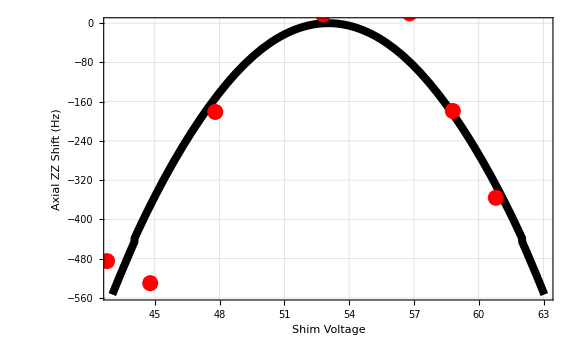

```mathematica
(*acutal data*)

(*known single Ca frequencies*)
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)

(*masses in ion chain*)
massArr = {mCaIon, mHCl35, mCaIon};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];

(*find where Hao took this data*)
actualVoltageList = {42.79, 62.79, 52.79, 44.79, 60.79, 47.8, 52.79, 57.8,55.79,52.79, 58.8, 56.8};
offsetSecFreqHz = {-485, -635, 18, -530, -356, -181, 72, 31, 82, 28, -179, 20};


(*Collect and process data*)
actualData = Transpose@{actualVoltageList, offsetSecFreqHz};
voltRange = Max[actualVoltageList]-Min[actualVoltageList];
voltMidPoint = Mean[actualVoltageList];

(*fit data to parabola*)
nlm = NonlinearModelFit[actualData, -a*(x-b)^2+c,{a,b,c}, x, MaxIterations->1000];
voltMidPoint = ({a,b,c}/. nlm["BestFitParameters"])[[2]];

(*magic number from what I understand - close to guggenmos thesis I think*)
κProjection = 1.8;
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
secFreqs = Table[getAxialRock[getSecFreqs[{(κProjection*(Volt-voltMidPoint))/Sqrt[2],(κProjection*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


AxialZZStrayFieldPlot = Show[{Plot[(getAxialRock[getSecFreqs[{(κProjection*(Voltage-voltMidPoint))/Sqrt[2],(κProjection*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, mCaIon, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}],
ListPlot[Transpose@{actualVoltageList, offsetSecFreqHz}, PlotStyle->{Red, PointSize[0.02]}]},
FrameLabel->{Style["Shim Voltage", 16], Style["Axial ZZ Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

```mathematica
Export["C:\\Users\\joshr\\OneDrive\\Documents\\UCLA\\Research\\Presentations\\2026\\Erics_Muri\\images\\axial_zz_shift_stray_field\\axial_zz_shift_strya_field.jpg", AxialZZStrayFieldPlot, 
LightDark -> "Light"];
```

### Axial OOP mode shift of Ca - HCl chain (see 09/10 data)

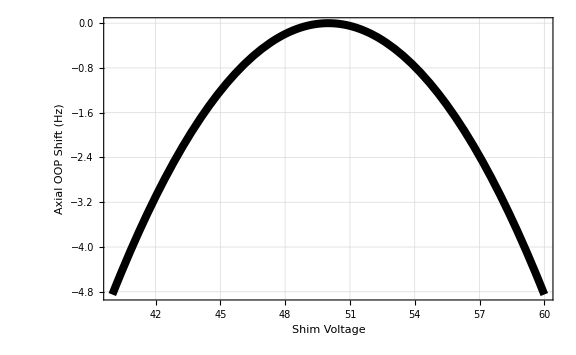

```mathematica
(*known single Ca frequencies*)
knownSecFreqs = 2*π*MHz*{.7116, 1.706, 1.932}; 

(*masses in ion chain*)
massArr = {mH2Cl37,mCaIon};
numIons = Length[massArr]; 
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];

(*Collect and process data*)
voltRange = 20;
voltMidPoint = 50;
voltageList = Range[-voltRange/2+voltMidPoint,voltRange/2+voltMidPoint]; 

(*magic number from what I understand - close to guggenmos thesis I think*)
κProjection = 1.8;
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
maxSecFreq = Max[secFreqs];
getSecFreqs[{0,0,0}, massArr, knownSecFreqs, mCaIon, numIons, ionPositions][[2]][[2]];
secFreqs = Table[getSecFreqs[{(κProjection*(Volt-voltMidPoint))/Sqrt[2],(κProjection*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, mCaIon, numIons, ionPositions][[2]][[2]], {Volt, voltageList}];


AxialOOPStrayFieldPlot = Show[{
Plot[(getSecFreqs[{(κProjection*(Voltage-voltMidPoint))/Sqrt[2],(κProjection*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, mCaIon, numIons, ionPositions][[2]][[2]]- Max[secFreqs])*MHz,
{Voltage, Min[voltageList], Max[voltageList]}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Shim Voltage", 16], Style["Axial OOP Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

### Axial COM Mode Shift

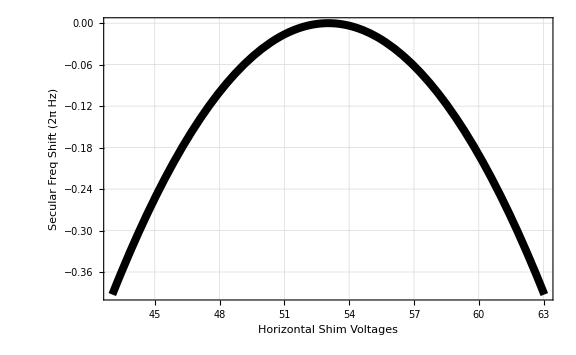

```mathematica
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
secFreqs = Table[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[1]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];

Show[{Plot[(getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[1]]- maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (2π Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

## Axial Rocking Mode Shift Dependence on Single Ion Secular Frequencies

### Scan Wide Range of Secular Frequencies

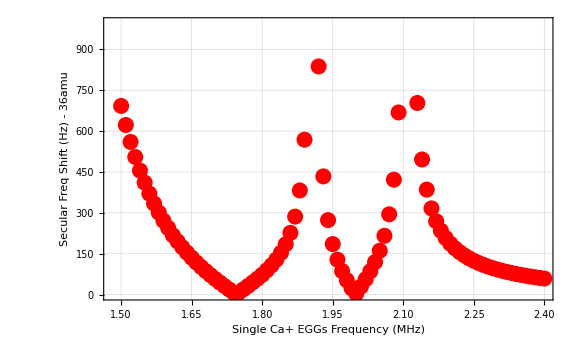

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 2.22, 2.4};
knownMass = 39.962590863; 
mUnknown = 36;
massArr = {knownMass, mUnknown, knownMass};
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.500, 2.40,.01}];
freqShift = Table[[.71,eggsFreq-.2,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
mass36Plot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz) - 36amu", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.93-.05, 1.93}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

1.22976: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.64332: {0.57476,0,0,-0.582496,0,0,0.57476,0,0}

1.70236: {0,-0.577948,0,0,0.576154,0,0,-0.577948,0}

1.74078: {-0.707107,0,0,0,0,0,0.707107,0,0}

1.77196: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

1.79466: {0,-0.707107,0,0,0,0,0,0.707107,0}

1.99239: {-0.411887,0,0,-0.812834,0,0,-0.411887,0,0}

2.04305: {0,-0.407402,0,0,-0.817341,0,0,-0.407402,0}

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\axial_zz_stray_field_shift36.jpg", mass36Plot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\axial_zz_stray_field_shift36.jpg

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
massArr = {knownMass, mUnknown, knownMass};
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.200, 3.000,.05}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.23,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
mass39Plot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz) - 39amu", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

-Graphics-

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\axial_zz_stray_field_shift39.jpg", mass39Plot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\axial_zz_stray_field_shift39.jpg

### Scan Narrowly about “nulls” where shift vanishes

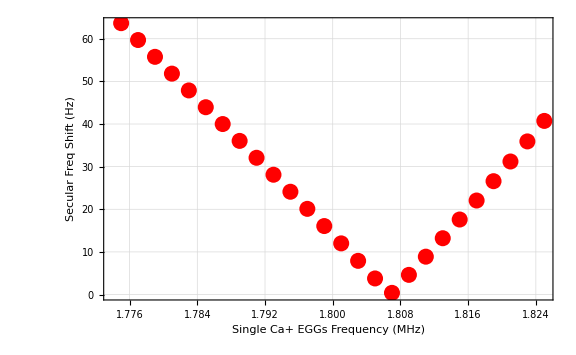

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.775, 1.825,.002}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
firstNullPlot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\first_null_plot.jpg", firstNullPlot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\first_null_plot.jpg

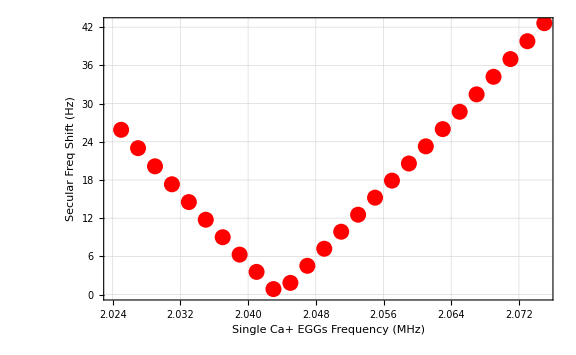

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 2.025, 2.075,.002}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
secondNullPlot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

#### Scan narrowly about ‘resonances’

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\second_null_plot.jpg", secondNullPlot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\second_null_plot.jpg

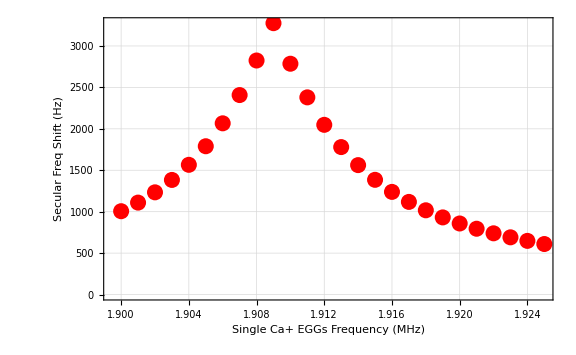

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.9, 1.925,.001}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

### See trend of stray fields and shift caused for different secular frequency configurations

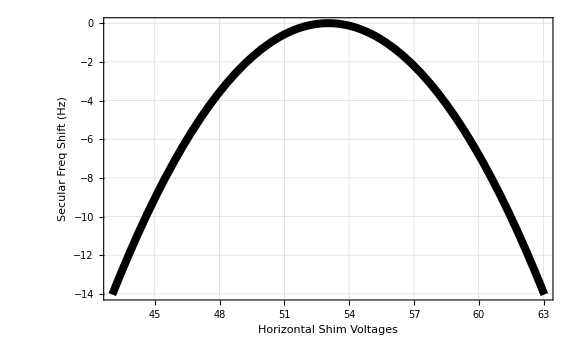

```mathematica
testSecFreqs = 2*π*{.71, 1.5, 1.8}*MHz;
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

```mathematica
testSecFreqs = 2*π*{.71, 1.8, 2.1}*MHz;
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

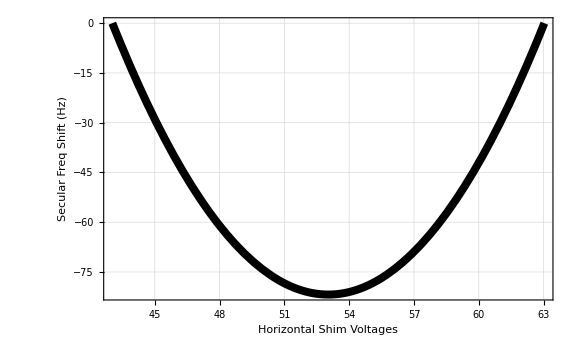

## Coulomb Anharmonic Calculations

### Initialization Code

```mathematica
ll[q_, secFreqsMHz_]:= Sqrt[ℏ/(2*2*π*secFreqsMHz[[q]]*MHz)];
quarticDiagonalTerms[nList_, G4_,  secFreqsMHz_, numModes_]:=Sum[ll[i,secFreqsMHz]^4*G4[[i,i,i,i]]*(6*nList[[i]]^2+6*nList[[i]]+3), {i,1,numModes}]
quarticOffDiagonalTerms[nList_, G4_,  secFreqsMHz_, numModes_]:=Sum[6*ll[i, secFreqsMHz]^2*ll[j, secFreqsMHz]^2*G4[[i,i,j,j]]*(2*nList[[i]]+1)*(2*nList[[j]]+1), 
													{i,1,numModes-1},
													{j,i+1,numModes}]
firstOrderPert[nList_, G4_, secFreqsMHz_, numModes_]:= (quarticDiagonalTerms[nList, G4,  secFreqsMHz, numModes] 
													+ quarticOffDiagonalTerms[nList, G4,  secFreqsMHz, numModes]);
```

```mathematica
(*Construct Matrix Elements*)
x3Element[m_, n_]:= (Sqrt[(n+1)*(n+2)*(n+3)]*KroneckerDelta[m, n+3]
								+3*(n+1)^(3/2)*KroneckerDelta[m, n+1]
								+ 3*n^(3/2)*KroneckerDelta[m, n-1]
								+ Sqrt[(n)*(n-1)*(n-2)]*KroneckerDelta[m, n-3]
								);
x2Element[m_, n_]:= (Sqrt[(n+1)*(n+2)]*KroneckerDelta[m,n+2]
					+ (2*n+1)*KroneckerDelta[m, n]
					+ Sqrt[n*(n-1)]*KroneckerDelta[m, n-2]
					);								
x1Element[m_, n_]:= Sqrt[n+1]KroneckerDelta[m,n+1] + Sqrt[n]*KroneckerDelta[m,n-1];	

				
(*Construct Amplitudes*)											
cubicDiagonalTerm[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= Sum[G3[[i,i,i]]*ll[i, secFreqsMHz]^3*
										x3Element[mList[[i]], nList[[i]]]*
										Product[KroneckerDelta[mList[[q]], nList[[q]]], {q, DeleteCases[Range[numModes], i]}]
										,
										{i, 1, numModes}];
cubicOffDiagonalTerm[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= (Sum[3*G3[[i,j,j]]*ll[j, secFreqsMHz]^2*ll[i,secFreqsMHz]
										* x1Element[mList[[i]], nList[[i]]]
										* x2Element[mList[[j]], nList[[j]]]
										* Product[
									        KroneckerDelta[mList[[q]], nList[[q]]],
									        {q, Complement[Range[numModes], {i, j}]}]
									    + 3*G3[[i,i,j]]*ll[i, secFreqsMHz]^2*ll[j, secFreqsMHz]*
										x1Element[mList[[j]], nList[[j]]]* x2Element[mList[[i]], nList[[i]]]
										*  Product[
									        KroneckerDelta[mList[[q]], nList[[q]]],
									        {q, Complement[Range[numModes], {i, j}]}
									     ],
										{i, 1, numModes-1},
										{j, i+1, numModes}
										]
										+ 
										Sum[
										6*G3[[i,j,k]]*ll[i, secFreqsMHz]*ll[j, secFreqsMHz]*ll[k, secFreqsMHz]
										* x1Element[mList[[i]], nList[[i]]]
										* x1Element[mList[[j]], nList[[j]]] 
										* x1Element[mList[[k]], nList[[k]]]
										* Product[
								        KroneckerDelta[mList[[q]], nList[[q]]],
								        {q, Complement[Range[numModes], {i, j, k}]}],
										{i, 1, numModes-2},
										{j, i+1, numModes-1},
										{k, j+1, numModes}]
										);
										
cubicMatrixElement[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= (cubicDiagonalTerm[mList, nList, G3,  secFreqsMHz, numModes] 
																+ cubicOffDiagonalTerm[mList, nList, G3,  secFreqsMHz, numModes]);

secOrderPertEle[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= Abs[cubicMatrixElement[mList, nList, G3,  secFreqsMHz, numModes]]^2/(Total[ℏ*2*π*MHz*secFreqsMHz*nList]-Total[ℏ*2*π*MHz*secFreqsMHz*mList]);
secOrderPert[intermediateStates_, nList_, G3_,  secFreqsMHz_, numModes_]:=Sum[
secOrderPertEle[mList, nList, G3,  secFreqsMHz, numModes], 
{mList, intermediateStates}
]
```

```mathematica
(*Create all connected basis states to a nList*)

createCandidateStates[nList_, numModes_]:=Module[{states},
	states = {};
	(*x3 term all excitations on one mode*);
	Do[
	states = Join[states, 
	Table[
	nList+d*UnitVector[numModes, q], 
	{d, {-3,-1,1,3}}
	]
	],
	{q, 1, numModes}
	];
	(*1 x2 term and 1 x1 term - two excitations on one mode and one excitations one another mode*)
	Do[
	states = Join[states, 
	Catenate @ Table[
	nList
	+di*UnitVector[numModes, q1]
	+dj*UnitVector[numModes, q2],
	{di, {-2,0,2}},
	{dj, {-1,1}}
	]
	],
	{q1, 1, numModes-1},
	{q2, q1+1, numModes}
	];
	Do[
	states = Join[states, 
	Catenate @ Table[
	nList
	+di*UnitVector[numModes, q2]
	+dj*UnitVector[numModes, q1],
	{di, {-2,0,2}},
	{dj, {-1,1}}
	]
	],
	{q1, 1, numModes-1},
	{q2, q1+1, numModes}
	];
	(*3 x1 terms -  all excitations on different modes*);
	Do[
	states = Join[states, 
	Catenate @ Catenate @ Table[
	nList
	+di*UnitVector[numModes, q1]
	+dj*UnitVector[numModes, q2]
	+dk*UnitVector[numModes, q3],
	{di, {-1,1}},
	{dj, {-1,1}},
	{dk, {-1,1}}
	]
	],
	{q1, 1, numModes-2},
	{q2, q1+1, numModes-1},
	{q3, q2+1, numModes}
	];
	states = Select[states, Min[#]>=0 &];
	DeleteDuplicates[states]
	]
```

```mathematica
getPerturbationTensors[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, β_:0]:=
 Module[
 {massIndepMathieuParams, massIndepSecFreqs, U, evecsNormalized, secFreqsMHz, ionEqPositions,
 coordMasses, U3, A3, A4, B3temp, C3temp, U4, B4temp, C4temp, D4temp, G3, G4},
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, β];
coordMasses=Flatten[ConstantArray[#,Length[First[ionPositions]]]&/@ massArr] *amu;
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions] (*this must be a different name*);
{evecsNormalized, secFreqsMHz} = getModeParams[U, massArr, ionEqPositions, numIons,ionPositions];
U3 = D[U, {Flatten[ionPositions], 3}]/.ionEqPositions;
U4 = D[U, {Flatten[ionPositions], 4}]/.ionEqPositions;
A3 = U3/(3! Sqrt[Outer[Times, coordMasses, coordMasses, coordMasses]]);
A4 = U4/(4! Sqrt[Outer[Times, coordMasses, coordMasses, coordMasses, coordMasses]]);

B3temp = TensorContract[TensorProduct[A3, evecsNormalized], {{1, 5}}];
C3temp = TensorContract[TensorProduct[B3temp, evecsNormalized], {{1, 5}}];
G3 = TensorContract[TensorProduct[C3temp, evecsNormalized], {{1, 5}}];

B4temp = TensorContract[TensorProduct[A4, evecsNormalized], {{1, 6}}];
C4temp = TensorContract[TensorProduct[B4temp, evecsNormalized], {{1, 6}}];
D4temp = TensorContract[TensorProduct[C4temp, evecsNormalized], {{1, 6}}];
G4 = TensorContract[TensorProduct[D4temp, evecsNormalized], {{1, 6}}];
{G3, G4, secFreqsMHz}
]
```

```mathematica
calcSecFreqShifts[nList_, q_, G3_, G4_, secFreqsMHz_]:= Module[
{intermediateStates, intermediateStatesExcited, excitedState, shift, numModes},
	numModes = Length[nList];
	excitedState = nList + UnitVector[numModes, q];
	intermediateStates = DeleteCases[createCandidateStates[nList, numModes], nList];
	intermediateStatesExcited = DeleteCases[createCandidateStates[excitedState, numModes], excitedState];
	shift = 
	(firstOrderPert[excitedState, G4, secFreqsMHz, numModes] + secOrderPert[intermediateStatesExcited, excitedState, G3, secFreqsMHz, numModes]) /(2*π*ℏ) 
	- (firstOrderPert[nList, G4, secFreqsMHz, numModes] + secOrderPert[intermediateStates, nList, G3, secFreqsMHz, numModes]) /(2*π*ℏ)
]
```

```mathematica
getSecFreqShifts[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, nList_, q_:1, β_:0]:=
 Module[
 {shift, G3, G4, secFreqsMHz},
 {G3, G4, secFreqsMHz} = getPerturbationTensors[EField, 
	massArr, knownSecFreqs, knownMass, numIons, ionPositions, β];
shift = calcSecFreqShifts[nList, q, G3, G4, secFreqsMHz]
]
```

### Check Roos (https://arxiv.org/pdf/0705.0788)

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
knownSecFreqs = 2*π*MHz*{1.7, 4, 4}; 
massArr = {knownMass, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
nList = {0,0,0,0,0,0};
```

```mathematica
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

1.7: {0,0,0.707107,0,0,0.707107}

2.94449: {0,0,-0.707107,0,0,0.707107}

3.62077: {0.465608,-0.532174,0,-0.465608,0.532174,0}

3.62077: {0.532174,0.465608,0,-0.532174,-0.465608,0}

4.: {-0.514148,-0.48544,0,-0.514148,-0.48544,0}

4.: {-0.48544,0.514148,0,-0.48544,0.514148,0}

{-2.605,-4.28582,-6.03923,-10.0395,-15.9123}

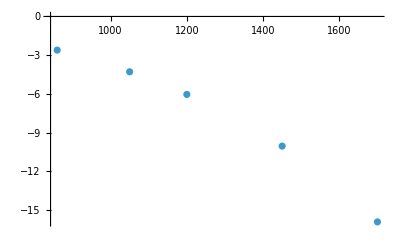

```mathematica
axialSecFreqs = {.86, 1.05, 1.2, 1.45, 1.7};
secShifts = Table[getSecFreqShifts[EField, 
massArr, 2*π*MHz*{axialSecFreqs[[s]], 4, 4}, knownMass, numIons, ionPositions,nList + UnitVector[6,3], 2,0]- 
getSecFreqShifts[EField, massArr, 2*π*MHz*{axialSecFreqs[[s]], 4, 4}, knownMass, numIons, ionPositions,nList, 2,0],{s, 1, Length[axialSecFreqs]}]
a = Thread[{axialSecFreqs(kHz), secShifts}];
ListPlot[a]
```

### Secular Frequency Shift for Ca - H35Cl - Ca as we Heat Chain

```mathematica
knownMass = mCaIon; 
mUnknown = mHCl35;
knownSecFreqs = 2*π*MHz*{.721, 2.240, 2.419}; 
massArr = {knownMass, knownMass, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.08204 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721: {0,0,0.57735,0,0,0.57735,0,0,0.57735}

1.24881: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.7364: {0,0,-0.408248,0,0,0.816497,0,0,-0.408248}

1.94164: {-0.408248,0,0,0.816497,0,0,-0.408248,0,0}

2.12079: {0.707107,0,0,0,0,0,-0.707107,0,0}

2.14568: {0,0.408248,0,0,-0.816497,0,0,0.408248,0}

2.24: {-0.57735,0,0,-0.57735,0,0,-0.57735,0,0}

2.30905: {0,0.707107,0,0,0,0,0,-0.707107,0}

2.419: {0,-0.57735,0,0,-0.57735,0,0,-0.57735,0}

#### Axial Stretch/Zigzag (1,-1,1) Mode

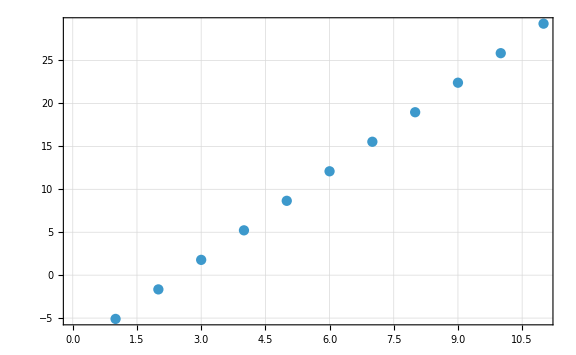

```mathematica
knownSecFreqs = 2*π*MHz*{.721, 2.240, 2.419}; 
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 3], 3,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

#### Axial COM (1,1,1) Mode

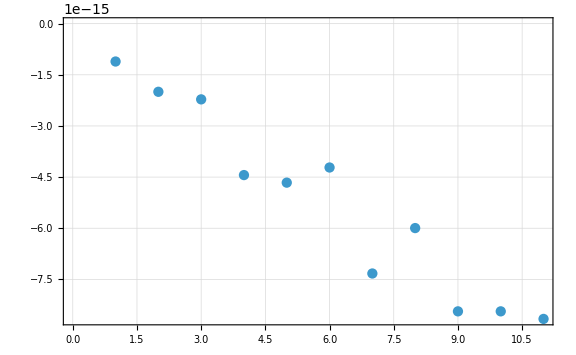

```mathematica
knownSecFreqs = 2*π*MHz*{.721, 2.240, 2.419};
nList = ConstantArray[0,9];
secShiftsCOM = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 1], 1,0],{s, 0,nMax}];
secShiftsCOMPlot = Labeled[ListPlot[secShiftsCOM],
{"Axial COM Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

```mathematica
Export["C:\\Users\\joshr\\OneDrive\\Documents\\UCLA\\Research\\Presentations\\2026\\Erics_Muri\\images\\sec_freq_shift_phonons\\axial_com_shift.jpg", secShiftsCOMPlot]
```

C:\Users\joshr\OneDrive\Documents\UCLA\Research\Presentations\2026\Erics_Muri\images\sec_freq_shift_phonons\axial_com_shift.jpg

### Secular Frequency Shift for Ca - H_2 ^37Cl - Ca as we Heat Chain

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.712858: {0,0,0.58064,0,0,0.570713,0,0,0.58064}

0.774205: {0.431016,0,0,-0.792748,0,0,0.431016,0,0}

1.11777: {0.707107,0,0,0,0,0,-0.707107,0,0}

1.20399: {0,-0.435707,0,0,0.787603,0,0,-0.435707,0}

1.22976: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.33945: {-0.560558,0,0,-0.609549,0,0,-0.560558,0,0}

1.44455: {0,0.707107,0,0,0,0,0,-0.707107,0}

1.62456: {0,-0.55692,0,0,-0.616183,0,0,-0.55692,0}

1.72394: {0,0,-0.403555,0,0,0.82115,0,0,-0.403555}

#### Axial Stretch/Zigzag (1,-1,1) Mode

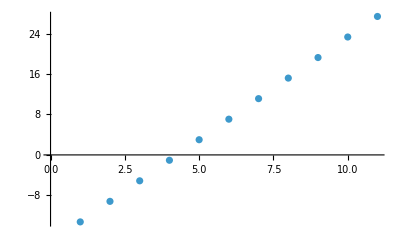

```mathematica
knownSecFreqs = 2*π*MHz*{.81, 1.3242, 1.6096};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 9], 9,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

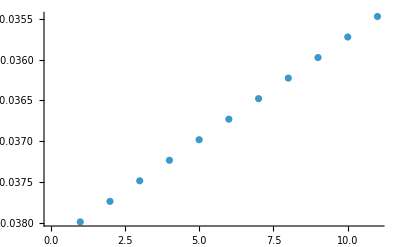

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 2.2, 2.4};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 9], 9,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

#### Axial COM (1,1,1) Mode

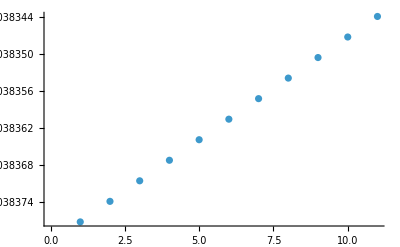

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 2.2, 2.4};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsCOM = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 1], 1,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsCOM],
{"Axial COM Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

### Dispersive Shift Calculations, i.e. how radial mode phonons affect axial stretch/COM mode

```mathematica
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

0.83944: {0.507896,0,0,-0.695761,0,0,0.507896,0,0}

1.08899: {0.707107,0,0,0,0,0,-0.707107,0,0}

1.22976: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.25658: {0,-0.526166,0,0,0.668055,0,0,-0.526166,0}

1.38096: {0.491977,0,0,0.718273,0,0,0.491977,0,0}

1.42044: {0,0.707107,0,0,0,0,0,-0.707107,0}

1.66966: {0,-0.472386,0,0,-0.744112,0,0,-0.472386,0}

1.77196: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
numPhonons = 3;
allModesCooled = {0,0,0,0,0,0,0,0,0};
radialModesHot = numPhonons*{0,1,1,0,1,1,1,1,0};
getSecFreqShifts[EField, 
massArr, knownSecFreqs, knownMass, numIons, ionPositions,allModesCooled , 9,0]- 
getSecFreqShifts[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions,radialModesHot, 9,0]
```

219.327

```mathematica
numPhonons = 6;
knownSecFreqs = 2*π*MHz*{.721, 2.240, 2.419};
allModesCooled = {0,0,0,0,0,0,0,0,0};
radialModesHot = numPhonons * {0,0,0,1,0,0,0,0,0};
getSecFreqShifts[EField, 
massArr, knownSecFreqs, knownMass, numIons, ionPositions,allModesCooled , 3,0]- 
getSecFreqShifts[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions,radialModesHot, 3,0]
```

37.4609

```mathematica
allModesCooled = {0,0,0,0,0,0,0,0,0};
radialRockModesHot = {0,0,0,3,3,3,0,3,0};
getSecFreqShifts[EField, 
massArr, knownSecFreqs, knownMass, numIons, ionPositions,allModesCooled , 9,0]- 
getSecFreqShifts[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions,radialRockModesHot, 9,0]
```

0.

```mathematica
allModesCooled = {0,0,0,0,0,0,0,0,0};
radialCOMModesHot = {0,0,0,0,0,3,0,3,0};
getSecFreqShifts[EField, 
massArr, knownSecFreqs, knownMass, numIons, ionPositions,allModesCooled , 9,0]- 
getSecFreqShifts[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions,radialCOMModesHot, 9,0]
```

4.01915

## Cubic Anharmonic Calculations (Normal modes of trapped ions in the presence of anharmonic trap potentials - https://arxiv.org/abs/1105.4752 ) Ions of same mass

### Ions of same mass

```mathematica
ωc[κ_, m_, λ_]:= Module[
{},
l = (qe/(8*π*e0*κ))^(1/3);
Sqrt[(2*qe*κ)/(m*amu)]*(1-9/2^(7/3)(l/λ)^2)]
ωs[κ_, m_, λ_]:= Module[
{},
l = (qe/(8*π*e0*κ))^(1/3);
Sqrt[(6*qe*κ)/(m*amu)]*(1-3/2^(7/3)(l/λ)^2)]
```

```mathematica
ωc[4.15, 40, 10^10]/(2*π)
ωs[4.15, 40, 10^10]/(2*π)
```

712.131

1233.45

```mathematica
(mCa*amu *(2*π*712*kHz)^2)/(2*qe)
```

4.14459×10^6

### Ions of unequal mass

```mathematica
ωp[κ_, μ_, m1_, λ_]:= Module[
{},
l = (qe/(8*π*e0*κ))^(1/3);
Sqrt[(2*qe*κ)/(m1*amu)]*Sqrt[1+μ+Sqrt[μ^2-μ+1]]*(1-3/2^(8/3)*(1-μ)/Sqrt[μ^2-μ+1]*l/λ)
]
ωm[κ_, μ_, m1_, λ_]:= Module[
{},
l = (qe/(8*π*e0*κ))^(1/3);
Sqrt[(2*qe*κ)/(m1*amu)]*Sqrt[1+μ-Sqrt[μ^2-μ+1]]*(1+3/2^(8/3)*(1-μ)/Sqrt[μ^2-μ+1]*l/λ)
]
```

```mathematica
(qe/(8*π*e0))1/l^3/.{l->20*μm}
```

89997.8

### Home’s Calculations

```mathematica
κh = 1.3*10^7;
ωm[κh, 1, 9, 10^10]/(2*π) (*Berylium ions*)
ωm[κh, 9/24,9,10^10]/(2*π)
ωp[κh, 9/24, 9, 10^10]/(2*π)
```

ωm[1.3×10^7,1,9,10000000000]/(2 π)

ωm[1.3×10^7,3/8,9,10000000000]/(2 π)

ωp[1.3×10^7,3/8,9,10000000000]/(2 π)

```mathematica
ωm[κh, 9/24, 9, 230*10^-6]/(2*π)-ωm[κh, 24/9, 24, 230*10^-6]/(2*π)
```

21017.3

### Our Results

```mathematica
ωz = 2*π*721.6*kHz;
mCa = knownMass;
κc = (mCa*amu*ωz^2)/(2*qe)
ωm[κc, 1, 40, 10^10]/(2*π*MHz) (*Ca ions*)
ωm[κc, 40/39,40,10^10]/(2*π*MHz)
ωp[κc, 39/40, 40, 10^10]/(2*π*MHz)
```

4.25711×10^6

0.721262

0.725784

1.24148

```mathematica
FullSimplify[Solve[cubicShiftZZ[mIonLeft, mIonRight, 1/g3, κκ]==δ, g3], Assumptions->mLeft>0 && mRight > 0 && ω>0 && κκ > 0];
g3SolInvMeters = cubicLambdaSol[[1]][[1]][[2]]/.{mLeft->mIonLeft, mRight->mIonRight, δ->26, κκ->κc};
g3SolInvMillimeters = g3SolInvMeters/1000
```

-0.275783

```mathematica
1/g3SolInvMillimeters
```

-3.62604

#### Analyzing COM frequency shift from ^40Ca+ - H_2^37Cl+ and H_2^37Cl+ - ^40Ca+

```mathematica
cubicShiftCOM[leftMass_, rightMass_, λ3_, κ_]:=ωm[κ, leftMass/rightMass, leftMass, λ3]/(2*π)-ωm[κ, rightMass/leftMass, rightMass, λ3]/(2*π);
cubicShiftZZ[leftMass_, rightMass_, λ3_, κ_]:=ωp[κ, leftMass/rightMass, leftMass, λ3]/(2*π)-ωp[κ, rightMass/leftMass, rightMass, λ3]/(2*π);


(*Solve for predicted cubic anharmonicity*)
(*data from rids 165469 (Ca+ on right) and 165463 (Ca+ on left)
  H_{2} ^{37}Cl+ used as dark ion*)
mIonLeft = mCaIon; 
mIonRight = mH2Cl37; 
ionSwapFreqShift = -3*Hz;

cubicLambdaSol = FullSimplify[Solve[cubicShiftCOM[mIonLeft, mIonRight, 1/g3, κκ]==δ, g3], Assumptions->mLeft>0 && mRight > 0 && ω>0 && κκ > 0];

g3SolInvMeters = cubicLambdaSol[[1]][[1]][[2]]/.{mLeft->mIonLeft, mRight->mIonRight, δ->ionSwapFreqShift, κκ->κc};
g3SolInvMillimeters = g3SolInvMeters/1000

(*Propagate error*)
σfLeft = (0.0022)*kHz;
σfRight = (0.0025)*kHz;
σδ = Sqrt[σfLeft^2+σfRight^2]; (*find actual value*)


errorPropFactor = (D[cubicLambdaSol[[1]][[1]][[2]]/.{{mLeft->mIonLeft, mRight->mIonRight, κκ->κc}}, δ]/.{δ->ionSwapFreqShift})[[1]];

g3ErrorInvMeters = Sqrt[errorPropFactor^2*σδ^2];
g3ErrorInvMillimeters = g3ErrorInvMeters /1000

Print["Lower bound of length scale calculated at ", 1/(g3SolInvMillimeters + g3ErrorInvMillimeters), "mm"]
Print["Upper bound of length scale calculated at ", 1/(g3SolInvMillimeters - g3ErrorInvMillimeters), "mm"]
```

0.0318211

0.0353231

Lower bound of length scale calculated at 14.8933mm

Upper bound of length scale calculated at -285.545mm

### Calculating Shifts in Frequency from Anharmonicities

```mathematica
knownMass = mCaIon; 
mUnknown = mHCl35;
knownSecFreqs = 2*π*MHz*{.721, 2.240, 2.419}; 
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.08204 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.733114: {0,0,0.591051,0,0,0.548924,0,0,0.591051}

1.24881: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.79982: {0,0,0.388148,0,0,-0.835872,0,0,0.388148}

2.0653: {-0.621539,0,0,0.476842,0,0,-0.621539,0,0}

2.12079: {-0.707107,0,0,0,0,0,0.707107,0,0}

2.26262: {0,-0.629871,0,0,0.454451,0,0,-0.629871,0}

2.30905: {0,-0.707107,0,0,0,0,0,0.707107,0}

2.39674: {0.337178,0,0,0.878989,0,0,0.337178,0,0}

2.57889: {0,-0.321345,0,0,-0.890772,0,0,-0.321345,0}

```mathematica
knownMass = mCaIon; 

λ4 = 0.51*10^-3;
λ5 = 0.08*10^-3;
βExp = κc*(g3SolInvMeters + g3ErrorInvMeters); (*from above code, g3 is 1/λ3 which is easier to use for error propagation - make sure all secular frequencies are correct before calculating*)
γExp = κc / λ4^2;
δExp = 0;
knownSecFreqs = 2*π*MHz*{.7216, 2.297, 2.523}; 
massArr =  {mCaIon, mHCl35, mCaIon};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.08204 * MHz;
{evecsNormalized1, secFreqsMHz1} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions, 0, 0, 0];
{evecsNormalized2, secFreqsMHz2} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions, βExp,γExp, 0];
```

```mathematica
(secFreqsMHz2 - secFreqsMHz1)[[1]] *MHz
(secFreqsMHz2 - secFreqsMHz1)[[3]] *MHz
```

202.572

238.56

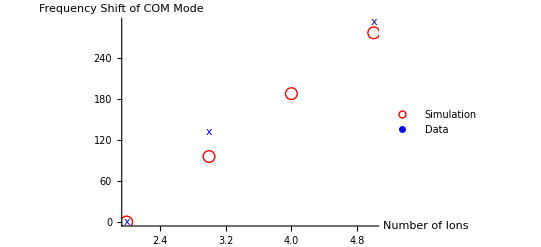

```mathematica
getAnharmonicShiftsCOM[EField_, 
knownSecFreqs_, knownMass_, numIons_, β_:0, γ_:0, δ_:0]:= Module[
{ionPositions, massArr },
massArr = knownMass*ConstantArray[1,numIons];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
massArr = knownMass*ConstantArray[1,numIons];
getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions, β, γ, δ][[2]][[1]]
]

simStyle = Directive[Red, PointSize[0.018]];
dataStyle = Directive[Blue, PointSize[0.018]];

simMarker = "○";
dataMarker = "x";

minIons = 2; 
maxIons = 5; 
anharmonicShiftsCOM = Table[getAnharmonicShiftsCOM[EField, knownSecFreqs, knownMass, numIons, βExp, γExp,0], {numIons, minIons, maxIons}];
anharmonicShiftsCOMReorigined = (anharmonicShiftsCOM - Min[anharmonicShiftsCOM]) *MHz;

simPlot = ListPlot[
					Thread[{Range[minIons, maxIons], anharmonicShiftsCOMReorigined}],
                     PlotStyle -> simStyle,
                       PlotMarkers -> {simMarker, 12},
                       PlotRange->All
                      ];

dataIons = {2,3,5};
data = {-0.2068, -0.0758, 0.0847};
dataReorigined = (data- Min[data])*kHz;
dataPlot = ListPlot[Thread[{dataIons, dataReorigined}],
					PlotStyle->dataStyle,
					PlotMarkers->dataMarker,
					PlotRange->All];

Legended[
 Show[
  simPlot,
  dataPlot,
  AxesLabel -> {"Number of Ions", "Frequency Shift of COM Mode"},
  Background -> White,
  BaseStyle -> Black,
  FrameStyle -> Black,
  AxesStyle -> Black,
 PlotRange -> All,
 PlotRangePadding -> Scaled[0.08]],
 Placed[
  PointLegend[
   {simStyle, dataStyle},
   {"Simulation", "Data"},
    LegendMarkers -> {simMarker, dataMarker}
   ],
  Right
  ]
 ]
```

### Ion Chain Image

```mathematica
ionImage = Import["C:\\Users\\joshr\\OneDrive\\Documents\\UCLA\\Research\\Code\\Mathematica-Code\\cat_interferometer\\ion_images\\E_Endcap_50_W_Endcap_69_Shims_On_RF_servo_lock_698.tif"];


knownSecFreqs = 2*π*MHz*{.348, 2.297, 2.523}; 
knownMass = mCaIon;
numIons = 13;
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
massArr = knownMass*ConstantArray[1, numIons];
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, βExp, γExp, 0];
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions];

ionAxialEqPositionsMicrons = Values[ionEqPositions[[1;;-1;;3]]]*10^6;

lineShift = 48.4;


sensorPixelSizeMicrons = 16; (*From an ANDOR iXon3 897 S/N: X-6959 peformance sheet on group drive*)
binning = 1;                  (* metadata from FITS image below gives vbin = 1 and h bin = 1*)
objectiveLensFocalLengthmm = 66.9; 
tubeLensFocalLengthmm = 1000.; (*Thorlabs ACT508-1000A*)
magnification = tubeLensFocalLengthmm / objectiveLensFocalLengthmm;     (*numbers from Grant' Thesis - pg 122*)

ionPlaneMicronsPerPixel = sensorPixelSizeMicrons*binning/magnification;
ionAxialEqPositionsPixels = ionAxialEqPositionsMicrons/ionPlaneMicronsPerPixel;


lines = Table[Line[{{ionAxialEqPositionsPixels[[i]] + lineShift, -250},{ionAxialEqPositionsPixels[[i]] + lineShift, 250}}],
{i,1,numIons}];

Show[{ionImage, Graphics[lines]},
ImageSize->Medium]
```

-Graphics-

```mathematica
ionImage = (ImageAdjust /@ Import["C:\\Users\\joshr\\OneDrive\\Documents\\UCLA\\Research\\Code\\Mathematica-Code\\cat_interferometer\\ion_images\\E_Endcap_50_W_Endcap_69_Shims_On_RF_servo_lock_698.fits"][[1]])[[1]];
metadata = Import["C:\\Users\\joshr\\OneDrive\\Documents\\UCLA\\Research\\Code\\Mathematica-Code\\cat_interferometer\\ion_images\\E_Endcap_50_W_Endcap_69_Shims_On_RF_servo_lock_698.fits","Metadata"];
ionImageTrimmed = ImageTrim[img, {{225, 250},{325, 300}}];

knownSecFreqs = 2*π*MHz*{.3474, 2.297, 2.523}; 
knownMass = mCaIon;
numIons = 13;
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
massArr = knownMass*ConstantArray[1, numIons];
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, βExp, γExp, 0];
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions];

ionAxialEqPositionsMicrons = Values[ionEqPositions[[1;;-1;;3]]]*10^6;

lineShift = 55.2;

cameraSN = metadata[1]["GENERAL INFORMATION"]["HIERARCH"]["SERIALNUMBER"][[1]]; 
Print["The Camera used was: ANDOR" cameraSN]

sensorPixelSizeMicrons = 16; (*From an ANDOR iXon3 897 S/N: X-6959 peformance sheet on group drive*)
vbin = metadata[1]["GENERAL INFORMATION"]["VBIN"][[1]];
hbin = metadata[1]["GENERAL INFORMATION"]["HBIN"][[1]];

binning = vbin * hbin; 
magnification = 1000/66.9;     (*numbers from Grant' Thesis - pg 122*)

ionPlaneMicronsPerPixel = sensorPixelSizeMicrons*binning/magnification;
ionAxialEqPositionsPixels = ionAxialEqPositionsMicrons/ionPlaneMicronsPerPixel;

lines = Table[Line[{{ionAxialEqPositionsPixels[[i]] + lineShift, -250},{ionAxialEqPositionsPixels[[i]] + lineShift, 250}}],
{i,1,numIons}];

Show[{ionImageTrimmed, Graphics[lines]},
ImageSize->Medium]
```

The Camera used was: ANDOR X-6959

-Graphics-

### See if we can do anharmonicity check by changing Ca place in three ion chain

```mathematica
knownMass = 39.962590863; 
λ3 = -17*10^-3;
λ4 = 0.47*10^-3;
λ5 = 0.08*10^-3;
βExp = κc / λ3;
γExp = κc / λ4^2;
δExp = 0;
knownSecFreqs = 2*π*MHz*{.7216, 2.297, 2.523}; 

EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.08204 * MHz;
```

```mathematica
massArr =  {mCaIon, mHCl35, mCaIon};
{evecsNormalized2, secFreqsMHz2} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions, βExp,γExp, 0];
secFreqsMHz2[[1]]
```

0.733968

```mathematica
massArr =  {mCaIon,  mCaIon, mHCl35};
{evecsNormalized3, secFreqsMHz3} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions, βExp, γExp, 0];
secFreqsMHz3[[1]]
```

0.73379

```mathematica
(secFreqsMHz3[[1]] - secFreqsMHz2[[1]])*MHz
```

-185.639

```mathematica
(secFreqsMHz3[[1]] - secFreqsMHz2[[1]])*MHz
```

-177.738

TensorContract::lvrank: Cannot contract level 5 because rank is 4.

$Aborted

0.